```mathematica
Series[y/(2+y), {y, 0, 6}]
```

y/2-y^2/4+y^3/8-y^4/16+y^5/32-y^6/64+O[y]^7

```mathematica
Series[Log[1+y/2], {y, 0, 6}]
```

y/2-y^2/8+y^3/24-y^4/64+y^5/160-y^6/384+O[y]^7

```mathematica
Series[y/(2+y)-Log[1+y/2], {y, 0, 6}]
```

-y^2/8+y^3/12-(3 y^4)/64+y^5/40-(5 y^6)/384+O[y]^7

```mathematica
Series[y^2/(2+y)^2, {y, 0, 6}]
```

y^2/4-y^3/4+(3 y^4)/16-y^5/8+(5 y^6)/64+O[y]^7

```mathematica
Series[y^4/(2+y)^4, {y, 0, 6}]
```

y^4/16-y^5/8+(5 y^6)/32+O[y]^7

```mathematica
Series[y^6/(2+y)^6, {y, 0, 6}]
```

y^6/64+O[y]^7

```mathematica
A[n_] := BernoulliB[n]*2^n/n;
```

```mathematica
A[2]
```

1/3

```mathematica
A[4]
```

-2/15

```mathematica
A[6]
```

16/63

```mathematica
g2[y_] := A[2]*y^2/(2+y)^2+A[4]*y^4/(2+y)^4+A[6]*y^6/(2+y)^6;
```

```mathematica
Series[g2[y], {y, 0, 6}]
```

y^2/12-y^3/12+(13 y^4)/240-y^5/40+(37 y^6)/4032+O[y]^7

```mathematica
Series[y/(2+y)-Log[1+y/2]+g2[y], {y, 0, 6}]
```

-y^2/24+(7 y^4)/960-(31 y^6)/8064+O[y]^7

```mathematica
g3[y_, m_] := Sum[A[2*i]*y^(2*i)/(2+y)^(2*i), {i, 1, m}];
```

```mathematica
Series[y/(2+y)-Log[1+y/2]+g3[y, 6], {y, 0, 10}]
```

-y^2/24+(7 y^4)/960-(31 y^6)/8064+(127 y^8)/30720-(511 y^10)/67584+O[y]^11

```mathematica
(*Fa[y_] := -y^2/24+7*y^4/960-31*y^6/8064+127*y^8/30720-511*y^10/67584;*)
Fa[y_] = Normal[Series[y/(2+y)-Log[1+y/2]+g3[y, 100], {y, 0, 102}]];
```

```mathematica
Fb[y_] := Log[1/y]-PolyGamma[1/2+1/y];
```

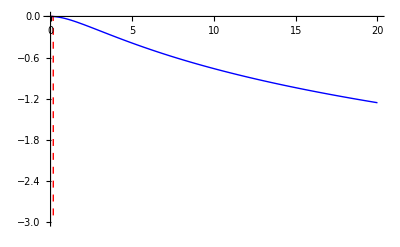

```mathematica
Show[Plot[Fa[y], {y, 0, 20},PlotStyle->{Red,Dashed,Thick},PlotRange->{{0,20},{-3,0}}],Plot[Fb[y], {y, 0, 20},PlotStyle->{Blue,Thick}]]
```

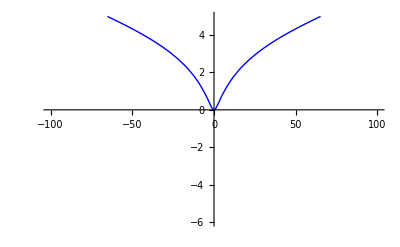

```mathematica
Plot[-2*Fb[Abs[y]]+(y/100)^2, {y, -100, 100},PlotStyle->{Blue,Thick}, PlotRange->{{-100,100},{-6,5}}]
```

```mathematica
F1 = fsoz + 2*fsox + fsz + 2*fsx+fe;
F2 = fsoz + 2*fsox + 2*fsx+fe;
F3 = 2*fsz + 4*fsx+fe;
F4 = 2*fsz + 4*fsox+fe;
```

```mathematica
Expand[Simplify[ExpandAll[F1^2*F3-F2^2*F4]]]
```

-4 fe^2 fsox-16 fe fsox^2-16 fsox^3-8 fe fsox fsoz-16 fsox^2 fsoz-4 fsox fsoz^2+4 fe^2 fsx-16 fsox^2 fsx+8 fe fsoz fsx+4 fsoz^2 fsx+16 fe fsx^2+16 fsox fsx^2+16 fsoz fsx^2+16 fsx^3+2 fe^2 fsz+4 fe fsox fsz+2 fe fsoz fsz+12 fe fsx fsz+16 fsox fsx fsz+8 fsoz fsx fsz+16 fsx^2 fsz+5 fe fsz^2+8 fsox fsz^2+4 fsoz fsz^2+12 fsx fsz^2+2 fsz^3